# Signal Processing - Project 1

## William Lewin & Elias Chahine wlewin@kth.se echahine@kth.se

## Part 1

### Assignment

A mobile station is moving along a straight line, away from a basestation at position x=0. The basestation antenna is at 30m above the ground and the mobile antenna is at 1.5 m. As seen by the picture the mobile is receiving two signals one direct ray and one reflected. Assume that the reflection is perfect which means no power loss at the reflection, but a phase shift of π.

Plot the squared amplitude (power) of the received signal when the mobile is moving from position x=0 to x=2km. Experiment with different types of graphs (e.g. log-scale, dB etc) to get a nice picture.

### Discussion

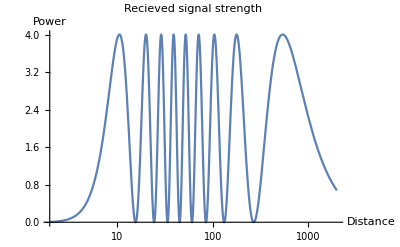
The problem at hand is to examine the effect of line-of-sight propagation of wireless signals.

When the car travels from 0 to 2000m away from the antenna, both the reflected and the direct signal changes. 

The recieved signal can be interpereted as the sum of both the reflected and the direct signal.

The following plot is a representation of both the reflected and the direct signal.

-Graphics-

### Code

```mathematica
ClearAll["`*"]
f=900*10^6; (*Frequency*)
c=299792458; (*Speed of light*)
ω=2*Pi*f;
th=30; (*Tower height*)
ch=1.5; (*Height of the car-antenna*)

(*Pythagoran theorem*)

(*Direct from tower to car: *)
distance1[x_]:=√((th-ch)^2+x^2);
(*Reflected from tower to car: *)
distance2[x_]:=√((th+ch)^2+x^2);


(* Time taken for the signal to reach the car at both signals *)
time1[x_]=distance1[x]/c;
time2[x_]= distance2[x]/c;
(*Direct signal*)
signal1[t_]:=ⅇ^(ⅉ(ω*t)); 
(*Reflected signal, Phase shifted direct signal*)
signal2[t_]:=ⅇ^(ⅉ(ω*t+Pi)); 

(*Recieved signal, from assignment*)
recieved[t_, x_]:=signal1[t-time1[x]]+signal2[t-time2[x]] ;

(*Remove imaginary part from signal*)
remove[x_]:=Simplify[ExpandAll[ⅇ^(-ⅉ*ω*t)recieved[t,x]]];
amplitude[x_]:=(Abs[remove[x]])^2;
LogLinearPlot[amplitude[x],{x,0,2000}, PlotLabel->"Recieved signal strength", AxesLabel->{"Distance", "Power"}]
```

-Graphics-

## Part 2

### Assignment

In this problem you shall examine the effect of sampling. Study the signal x[t_]:=Abs[Sin[2π f0 t]] where f_0=220Hz. 

Use the method Play and explain the sound by studying the complex FourierSeries.

Play the sound using the sampling frequency 8000Hz,What are the frequencies you will hear?

Play the sound using the sampling frequency 1000Hz. What frequencies will you hear now?

Draw the correct spectrum in these two cases.

### Discussion

### Code

```mathematica
ClearAll["`*"]
```

```mathematica
Subscript[f, 0]=220;
Subscript[t, 0]=1/Subscript[f, 0];
SetOptions[{FourierCoefficient,FourierCosCoefficient,FourierSinCoefficient},FourierParameters :>{1,2π/Subscript[t, 0]}];
x[t_]:=Abs[Sin[2*Pi*Subscript[f, 0]*t]];
Subscript[x, ak][k_]:= FourierCoefficient[x[t],t,k]
Subscript[x, fourier][t_,k_]:= FourierSeries[x[t],t,k]
```

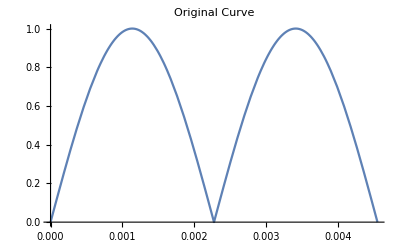

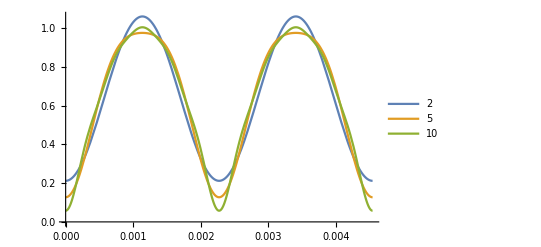

```mathematica
Plot[x[t],{t,0,Subscript[t, 0]},PlotLabel->"Original Curve"]
(*As the degree of Fourier series gets expanded, the curve gets more accurate*)
Plot[{Evaluate[Subscript[x, fourier][t,2]],Evaluate[Subscript[x, fourier][t,5]],Evaluate[Subscript[x, fourier][t,10]]},{t,0,Subscript[t, 0]},PlotLegends->{"2" ,"5","10"}]
```

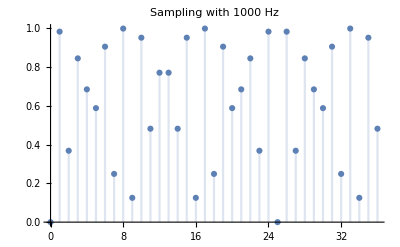

```mathematica
DiscretePlot[x[k/1000],{k,0,36},PlotLabel->"Sampling with 1000 Hz"]
```

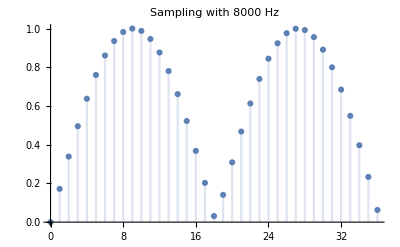

```mathematica
DiscretePlot[x[k/8000],{k,0,36},PlotLabel->"Sampling with 8000 Hz"]
```

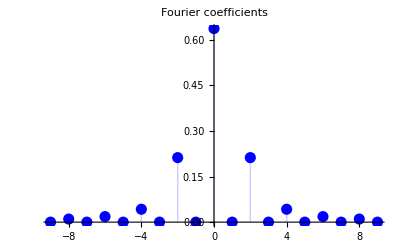

```mathematica
DiscretePlot[
Abs[Subscript[x, ak][k]],{k,-9,9},
PlotRange->All,PlotStyle->Directive[PointSize[0.02],Thick,Blue],
PlotLabel->"Fourier coefficients"
]
```

{{0,2/π},{440,-2/(3 π)},{-120,-2/(15 π)},{320,-2/(35 π)},{-240,-2/(63 π)},{200,-2/(99 π)},{-360,-2/(143 π)},{80,-2/(195 π)},{-480,-2/(255 π)},{-40,-2/(323 π)}}

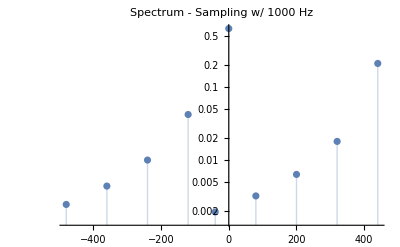

```mathematica
(*Spectrum for 1000 Hz Flerdimensionellt till en dimensionellt , absolute värdet av sinus kurva leder till dubbel frekvens*)
(* .// replace m med lösning för m, hoppar över värdet för k = 0, undersampling leads to ambiguious results*)
spectrum=Flatten[Table[{(k Subscript[f, 0]+1000m ),Subscript[x, ak][k]}/.Solve[Abs[k Subscript[f, 0]+1000m]≤1000/2,m,Integers],{k,0,18,2}],1]
ListLogPlot[Function[fa,{fa⟦1⟧,Abs[fa⟦2⟧]}]/@spectrum,PlotLabel->"Spectrum - Sampling w/ 1000 Hz",Filling->Axis]
```

{{0,2/π},{440,-2/(3 π)},{880,-2/(15 π)},{1320,-2/(35 π)},{1760,-2/(63 π)},{2200,-2/(99 π)},{2640,-2/(143 π)},{3080,-2/(195 π)},{3520,-2/(255 π)},{3960,-2/(323 π)}}

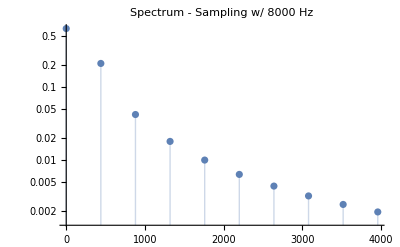

```mathematica
spectrum=Flatten[Table[{(k Subscript[f, 0]+8000m) ,Subscript[x, ak][k]}/.Solve[Abs[k Subscript[f, 0]+8000m]≤8000/2,m,Integers],{k,0,18,2}],1]
ListLogPlot[Function[fa,{fa⟦1⟧,Abs[fa⟦2⟧]}]/@spectrum,PlotLabel->"Spectrum - Sampling w/ 8000 Hz",Filling->Axis]
```